```mathematica
SetDirectory[NotebookDirectory[]]
dx=0.2;
dy=0.2;
buf=0;
xmax=16;
ymax=16;
xcm= Round[(2 xmax)/dx  +buf ]
ycm=Round[(2 ymax)/dy  +buf] 
FILESIZE = ( xcm*ycm)*8
FileByteCount["init/t00.bin"]

border=0;
X[i_]:=-xmax+(i-1-border) dx;
Y[j_]:=-ymax+(j-1-border) dy;

X[xcm/2+1]
 
dataXY[mat_]:={Table[{X[i],Y[j],mat[[i,j]]},{i,1,xcm},{j,1,ycm}]}
axesXY[text_]:={AxesLabel->{"X (in fm)","Y (in fm)","XY-PLANE"},PlotLabel->text<>" at η="<>ToString[0],LabelStyle->{Black,Bold},PlotStyle->{{White,Thick},{Red,Thick}},PlotRange->All,ImageSize->Large}
axesXY[text_,range_]:={AxesLabel->{"X (in fm)","Y (in fm)","XY-PLANE"},PlotLabel->text<>" at η="<>ToString[0],LabelStyle->{Black,Bold},PlotStyle->{{White,Thick},{Red,Thick}},PlotRange->range,ImageSize->Large}


τ0 = 0.2;
trace[mat_]:= mat[[1,1]]-mat[[2,2]]-mat[[3,3]]- τ0^2 mat[[4,4]]
dataXY[mat_]:={Table[{-xmax+(i-1)dx ,-ymax+(j-1) dy ,mat[[i,j]]},{i,1,xcm},{j,1,ycm}]};

axesXY[text_] := {AxesLabel->{"X (in fm)","Y (in fm)"},PlotLabel->text,LabelStyle->{Black,Bold},PlotStyle->{{White,Thick},{Red,Thick}},PlotRange->All};


GEVFM=0.1973;
E1 =(0.5028563305441270) ;
E2 =(1.62) ;
E3 =(1.86) ;
E4 =(9.9878355786273545)  ;
s95pP =Compile[{{en,_Real}},
Module[{ret,enfm},
enfm=en;
enfm *= GEVFM;
ret = Piecewise[{
{(0.3299*(E^(0.4346*enfm)-1)),enfm≤ E1},
{( 1.024 10^-7*E^(6.041*enfm)+0.007273+0.14578 enfm ),enfm>E1 && enfm≤E2},
{( 0.30195  E^(0.31308 enfm)-0.256232 ),enfm>E2&& enfm≤E3},
{(  0.332 enfm -0.3223 enfm^0.4585  +0.1167 enfm^-1.233 -0.003906 enfm E^(-0.05697 enfm) +0.1436 enfm E^(-0.9131*enfm) ),enfm>E3&& enfm≤E4},
{  ( 0.3327 enfm -0.3223 enfm^0.4585-0.003906 enfm E^(-0.05697 enfm)  ) ,enfm>E4}
}
];
ret/GEVFM
]
]
(*EIGEN VALUE SEARCH*)
entab=Table[0,{i,1,xcm},{j,1,ycm}];
vxtab=Table[0,{i,1,xcm},{j,1,ycm}];
vytab=Table[0,{i,1,xcm},{j,1,ycm}];
vztab=Table[0,{i,1,xcm},{j,1,ycm}];
p1tab=Table[0,{i,1,xcm},{j,1,ycm}];
p2tab=Table[0,{i,1,xcm},{j,1,ycm}];
p3tab=Table[0,{i,1,xcm},{j,1,ycm}];
p4tab=Table[0,{i,1,xcm},{j,1,ycm}];
p5tab=Table[0,{i,1,xcm},{j,1,ycm}]; 
Tμνtab=Table[0,{l,1,4},{m,1,4},{i,1,xcm},{j,1,ycm} ]; 
TμνIdealtab=Table[0,{l,1,4},{m,1,4},{i,1,xcm},{j,1,ycm} ]; 
Wμνtab=Table[0,{l,1,4},{m,1,4},{i,1,xcm},{j,1,ycm} ]; 
πμνtab=Table[0,{l,1,4},{m,1,4},{i,1,xcm},{j,1,ycm} ]; 
Πtab=Table[0,{l,1,4},{m,1,4},{i,1,xcm},{j,1,ycm} ]; 

mu1tab = Table[0,{i,1,xcm},{j,1,ycm}]; 
mu2tab = Table[0,{i,1,xcm},{j,1,ycm}]; 
epstab = Table[0,{i,1,xcm},{j,1,ycm}]; 

dxmu1tab = Table[0,{i,1,xcm},{j,1,ycm}]; 
dxmu2tab = Table[0,{i,1,xcm},{j,1,ycm}]; 
dxmu1mu2tab = Table[0,{i,1,xcm},{j,1,ycm}]; 

dymu1tab = Table[0,{i,1,xcm},{j,1,ycm}]; 
dymu2tab = Table[0,{i,1,xcm},{j,1,ycm}]; 
dymu1mu2tab = Table[0,{i,1,xcm},{j,1,ycm}]; 

axtab = Table[0,{i,1,xcm},{j,1,ycm}]; 
aytab = Table[0,{i,1,xcm},{j,1,ycm}]; 
bxtab = Table[0,{i,1,xcm},{j,1,ycm}]; 
bytab = Table[0,{i,1,xcm},{j,1,ycm}]; 

Istmpe1=OpenRead["init/mu1.bin",BinaryFormat->True] 
Istmpe2=OpenRead["init/mu2.bin",BinaryFormat->True] ;
Istmpe3=OpenRead["init/eps.bin",BinaryFormat->True] ;
Istmpe4=OpenRead["init/Dxmu1.bin",BinaryFormat->True]  ;
Istmpe5=OpenRead["init/Dxmu2.bin",BinaryFormat->True]  ;
Istmpe6=OpenRead["init/Dxmu1mu2.bin",BinaryFormat->True] ;
Istmpe7=OpenRead["init/Dymu1.bin",BinaryFormat->True] ;
Istmpe8=OpenRead["init/Dymu2.bin",BinaryFormat->True] ;
Istmpe9=OpenRead["init/Dymu1mu2.bin",BinaryFormat->True] ;
Istmpe10=OpenRead["init/ax.bin",BinaryFormat->True] ;
Istmpe11=OpenRead["init/ay.bin",BinaryFormat->True] ;
Istmpe12=OpenRead["init/bx.bin",BinaryFormat->True] ;
Istmpe13=OpenRead["init/by.bin",BinaryFormat->True] ; 
 
For[i=1,i<=xcm,i++,
For[j=1,j<=ycm,j++,
mu1tab[[i,j]]=BinaryRead[Istmpe1,"Real64"];
mu2tab[[i,j]]=BinaryRead[Istmpe2,"Real64"]; 
epstab[[i,j]]=BinaryRead[Istmpe3,"Real64"]; 
dxmu1tab[[i,j]]=BinaryRead[Istmpe4,"Real64"]; 
dxmu2tab[[i,j]]=BinaryRead[Istmpe5,"Real64"]; 
dxmu1mu2tab[[i,j]]=BinaryRead[Istmpe6,"Real64"]; 
dymu1tab[[i,j]]=BinaryRead[Istmpe7,"Real64"]; 
dymu2tab[[i,j]]=BinaryRead[Istmpe8,"Real64"];
dymu1mu2tab[[i,j]]=BinaryRead[Istmpe9,"Real64"]; 
axtab[[i,j]]=BinaryRead[Istmpe10,"Real64"];
aytab[[i,j]]=BinaryRead[Istmpe11,"Real64"];
bxtab[[i,j]]=BinaryRead[Istmpe12,"Real64"];
bytab[[i,j]]=BinaryRead[Istmpe13,"Real64"];
]
]

 Close[Istmpe1];
 Close[Istmpe2];
 Close[Istmpe3];
 Close[Istmpe4];
 Close[Istmpe5];
 Close[Istmpe6];
 Close[Istmpe7];
 Close[Istmpe8];
 Close[Istmpe9];
 Close[Istmpe10];
 Close[Istmpe11];
 Close[Istmpe12];
 Close[Istmpe13];
```

C:\Users\sidux\Google Drive\RESEARCH\MY CODE\NEWEST10

160

160

204800

204800

0.

CompiledFunction[…]

InputStream[…]

```mathematica
ListPlot3D[dataXY[mu1tab],axesXY["μ1"],PlotRange->All ] 
ListPlot3D[dataXY[mu2tab],axesXY["μ2"],PlotRange->All ]
ListPlot3D[dataXY[mu1tab mu2tab],axesXY["μ1μ2"],PlotRange->All ]
ListPlot3D[dataXY[dxmu1mu2tab],axesXY["∂_X (μ1μ2)"],PlotRange->All ]
ListPlot3D[dataXY[dymu1mu2tab],axesXY["∂_Y (μ1μ2)"],PlotRange->All ]
ListPlot3D[dataXY[axtab],axesXY["α^1"],PlotRange->All ]
ListPlot3D[dataXY[aytab],axesXY["α^2"],PlotRange->All ]
ListPlot3D[dataXY[bxtab],axesXY["β^1"],PlotRange->All ]
ListPlot3D[dataXY[bytab],axesXY["β^2"],PlotRange->All ]
```

-Graphics3D-

-Graphics3D-

-Graphics3D-

«6 more identical outputs»

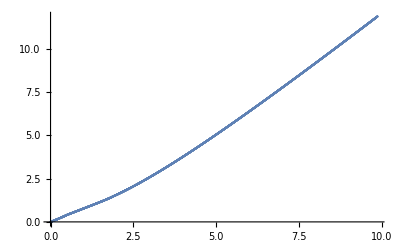

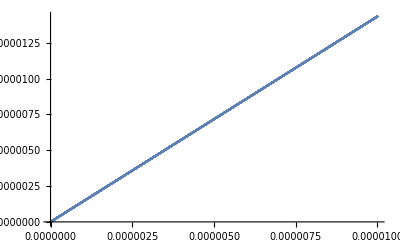

{m→0.143375,c→-1.02493×10^-13}

```mathematica
ListPlot[Table[{GEVFM a  ,s95pP[a]},{a,0,50,10^-2}]]  
ListPlot[Table[{ a  ,s95pP[a]},{a,10^-9,10^-5,10^-9}]] 
FindFit[Table[{a  ,s95pP[a]},{a,10^-9,10^-5,10^-10}], m x+c,{m,c},x]
```

```mathematica
Istmpe1=OpenRead["init/t00.bin",BinaryFormat->True] 
Istmpe2=OpenRead["init/t01.bin",BinaryFormat->True] ;
Istmpe3=OpenRead["init/t02.bin",BinaryFormat->True] ;
Istmpe4=OpenRead["init/t03.bin",BinaryFormat->True]  ;
Istmpe5=OpenRead["init/t11.bin",BinaryFormat->True]  ;
Istmpe6=OpenRead["init/t12.bin",BinaryFormat->True] ;
Istmpe7=OpenRead["init/t13.bin",BinaryFormat->True] ;
Istmpe8=OpenRead["init/t22.bin",BinaryFormat->True] ;
Istmpe9=OpenRead["init/t23.bin",BinaryFormat->True] ;
Istmpe10=OpenRead["init/t33.bin",BinaryFormat->True] ;
 
For[i=1,i<=xcm,i++,
For[j=1,j<=ycm,j++,
Tμνtab[[1,1,i,j]]=BinaryRead[Istmpe1,"Real64"];
Tμνtab[[1,2,i,j]]=BinaryRead[Istmpe2,"Real64"];
Tμνtab[[2,1,i,j]]=Tμνtab[[1,2,i,j]];
Tμνtab[[1,3,i,j]]=BinaryRead[Istmpe3,"Real64"];
Tμνtab[[3,1,i,j]]=Tμνtab[[1,3,i,j]];
Tμνtab[[1,4,i,j]]=BinaryRead[Istmpe4,"Real64"];
Tμνtab[[4,1,i,j]]=Tμνtab[[1,4,i,j]];
Tμνtab[[2,2,i,j]]=BinaryRead[Istmpe5,"Real64"]; 
Tμνtab[[2,3,i,j]]=BinaryRead[Istmpe6,"Real64"];
Tμνtab[[3,2,i,j]]=Tμνtab[[2,3,i,j]]  ;
Tμνtab[[2,4,i,j]]=BinaryRead[Istmpe7,"Real64"];
Tμνtab[[4,2,i,j]]=Tμνtab[[2,4,i,j]]  ; 
Tμνtab[[3,3,i,j]]=BinaryRead[Istmpe8,"Real64"];
Tμνtab[[3,4,i,j]]=BinaryRead[Istmpe9,"Real64"];
Tμνtab[[4,3,i,j]]=Tμνtab[[3,4,i,j]];
Tμνtab[[4,4,i,j]]=BinaryRead[Istmpe10,"Real64"];
]
]

 Close[Istmpe1];
 Close[Istmpe2];
 Close[Istmpe3];
 Close[Istmpe4];
 Close[Istmpe5];
 Close[Istmpe6];
 Close[Istmpe7];
 Close[Istmpe8];
 Close[Istmpe9]; Close[Istmpe10]
```

InputStream[…]

init/t33.bin

```mathematica
guu = {{1,0,0,0},{0,-1,0,0},{0,0,-1,0},{0,0,0,-1/τ0^2}};
gdd={{1,0,0,0},{0,-1,0,0},{0,0,-1,0},{0,0,0,-τ0^2}};
gud=  {{1,0,0,0},{0,1,0,0},{0,0,1,0},{0,0,0,1}}; 
For[i=1,i<=xcm,i++,
For[j=1,j<=ycm,j++, 
TμνField= Tμνtab[[All,All,i,j]];
X=-xmax+(i-1)*dx;
Y=-ymax+(j-1)*dy;
{vals,vecs}=Eigensystem[TμνField.gdd];
ikey=0;
index=-1;
Do[
If[
vecs[[  m,1 ]]==0,
Continue[];
,
vecs[[m]] = {1,vecs[[m,2]]/vecs[[m,1]], vecs[[m,3]]/vecs[[m,1]] ,vecs[[m,4]]/vecs[[m,1]]};
If[
Im[vecs[[  m,2 ]]  ]==0
&&Im[vecs[[  m,3]] ]==0
&&Im[vecs[[  m,4]] ]==0
&&Abs[vecs[[  m,2 ]] ]<1
&&Abs[vecs[[  m,3 ]] ]<1
&&Abs[vecs[[  m,4 ]] ]<1
&&Norm[{vecs[[  m,2 ]],vecs[[  m,3 ]],vecs[[  m,4 ]]}]<1
,
ikey++;
index=m;
];
];
,{m,1,4}];


If[ikey==1,
En=vals[[index]];
Vx=vecs[[index,2]];
Vy=vecs[[index,3]];
Vz=vecs[[index,4]];
,
Print[X];
Print[i];
Print[Y];
Print[j];
Print[vals];
Print[vecs[[1]]];
Print[vecs[[2]]];
Print[vecs[[3]]];
Print[vecs[[4]]];
Abort[]
];
 
G=1/(√(1-Vx^2-Vy^2-τ0^2 Vz^2));

u0=G;
u1=u0 Vx;
u2=u0 Vy;
u3=u0 Vz;
P=s95pP[En];
uupμ = {u0 ,u1 , u2 ,u3  };
udoμ= {u0 ,-u1 , -u2 ,-τ0^2 u3 };
dud = gud -Outer[Times,uupμ,udoμ] ;
duu = guu-Outer[Times,uupμ,uupμ];
TμνIdeal=((En+P ) Outer[Times, uupμ,uupμ] - P  guu );
TμνIdealtab[[All,All,i,j]] = TμνIdeal ; 
Wμ=dud.(udoμ.TμνField);
Wμν= Outer[Times, Wμ,uupμ]+Outer[Times, uupμ,Wμ];
Wμνtab[[All,All,i,j]] = Wμν;

PI = (trace[TμνField]-trace[TμνIdeal]-trace[Wμν])/3;

PIμν= PI duu;
Πtab[[All,All,i,j]]=PIμν ;

πμνtab[[All,All,i,j]] =  TμνField- TμνIdeal-Wμν-PIμν;

entab[[i,j]]=En;
vxtab[[i,j]]=Vx;
vytab[[i,j]]=Vy;
vztab[[i,j]]=Vz;
PItab[[i,j]]=PI;
 
]
]
```

```mathematica
X=0;
Y=0;
i=IntegerPart[(X+xmax)/dx +1]
j=IntegerPart[(Y+ymax)/dy +1]

MatrixForm[Tμνtab[[All,All,i,j]]]
MatrixForm[TμνIdealtab[[All,All,i,j]]]
MatrixForm[Wμνtab[[All,All,i,j]]]
MatrixForm[Πtab[[All,All,i,j]]]
MatrixForm[πμνtab[[All,All,i,j]]]

Print["******  TRACES ********"]

trace[Tμνtab[[All,All,i,j]]]
trace[TμνIdealtab[[All,All,i,j]]]
trace[Wμνtab[[All,All,i,j]]]
trace[Πtab[[All,All,i,j]]]
trace[πμνtab[[All,All,i,j]]]
(*

ListPlot3D[Wμνtab[[1,1]]]*)
```

81

81

(1530.7 | 0. | 0. | 4.51905×10^-12
0. | -4.54871 | 0. | -234.864
0. | 0. | -4.54871 | 0.
4.51905×10^-12 | -234.864 | 0. | 38494.9)

(1530.7 | 1.82873×10^-14 | 0. | 2.97078×10^-12
1.82873×10^-14 | 486.865 | 0. | 2.69273×10^-29
0. | 0. | 486.865 | 0.
2.97078×10^-12 | 2.69273×10^-29 | 0. | 12171.6)

(2.65753×10^-28 | -3.31322×10^-29 | 0. | 1.95655×10^-43
-3.31322×10^-29 | -6.00624×10^-46 | 0. | -4.87857×10^-44
0. | 0. | 0. | 0.
1.95655×10^-43 | -4.87857×10^-44 | 0. | 0.)

(0. | 2.11809×10^-16 | 0. | 3.44085×10^-14
2.11809×10^-16 | 23.3681 | 0. | 3.11881×10^-31
0. | 0. | 23.3681 | 0.
3.44085×10^-14 | 3.11881×10^-31 | 0. | 584.201)

(-4.54747×10^-13 | -1.84991×10^-14 | 0. | 1.51386×10^-12
-1.84991×10^-14 | -514.782 | 0. | -234.864
0. | 0. | -514.782 | 0.
1.51386×10^-12 | -234.864 | 0. | 25739.1)

******  TRACES ********

4.54747×10^-13

70.1042

2.65753×10^-28

-70.1042

2.27374×10^-13

```mathematica
ListPlot3D[dataXY[entab],axesXY["en"]]
ListPlot3D[dataXY[vxtab],axesXY["vx"]]
ListPlot3D[dataXY[vytab],axesXY["vy"]]
ListPlot3D[dataXY[vztab],axesXY["vz"]]
ListPlot3D[dataXY[πμνtab[[1,1]]],axesXY["π^00"]]
ListPlot3D[dataXY[πμνtab[[1,2]]],axesXY["π^01"]]
ListPlot3D[dataXY[πμνtab[[1,3]]],axesXY["π^02"]]
ListPlot3D[dataXY[πμνtab[[1,4]]],axesXY["π^03"]]
ListPlot3D[dataXY[πμνtab[[2,2]]],axesXY["π^11"]]
ListPlot3D[dataXY[πμνtab[[2,3]]],axesXY["π^12"]] 
ListPlot3D[dataXY[πμνtab[[2,4]]],axesXY["π^13"]] 
ListPlot3D[dataXY[πμνtab[[3,3]]],axesXY["π^22"]]
ListPlot3D[dataXY[πμνtab[[3,4]]],axesXY["π^23"]]
ListPlot3D[dataXY[πμνtab[[4,4]]],axesXY["π^33"]]
```

-Graphics3D-

-Graphics3D-

-Graphics3D-

«11 more identical outputs»